```mathematica
ClearAll[GradientDescent];

Options[GradientDescent]={"Restarts"->20,"MaxIterations"->500,"LearningRate"->0.02,"GradientStep"->10^-6,"Tolerance"->10^-8,"Method"->"Adam",(*"Adam" or "GD"*)"Momentum"->0.9,(*used for GD*)"Beta1"->0.9,(*Adam*)"Beta2"->0.999,(*Adam*)"Epsilon"->10^-8,(*Adam numerical stabilizer*)"NoiseScale"->0.0,(*optional random perturbation*)"NoiseEvery"->Infinity,(*perturb every k steps*)"InitialPoints"->Automatic,"Seed"->Automatic,"History"->True};

GradientDescent::badinit="Option \"InitialPoints\" must be Automatic, a vector of length n, or a matrix of starting points.";

GradientDescent[loss_,n_Integer?Positive,opts:OptionsPattern[]]:=Module[{restarts,maxIter,lr,h,tol,method,momentum,beta1,beta2,eps,noiseScale,noiseEvery,initPoints,seed,keepHistory,clamp,finiteRealQ,safeLoss,numericalGradient,makeStartPoints,runOne,starts,runs,best},restarts=OptionValue["Restarts"];
maxIter=OptionValue["MaxIterations"];
lr=OptionValue["LearningRate"];
h=OptionValue["GradientStep"];
tol=OptionValue["Tolerance"];
method=OptionValue["Method"];
momentum=OptionValue["Momentum"];
beta1=OptionValue["Beta1"];
beta2=OptionValue["Beta2"];
eps=OptionValue["Epsilon"];
noiseScale=OptionValue["NoiseScale"];
noiseEvery=OptionValue["NoiseEvery"];
initPoints=OptionValue["InitialPoints"];
seed=OptionValue["Seed"];
keepHistory=OptionValue["History"];
If[seed=!=Automatic,SeedRandom[seed]];
clamp[x_]:=Clip[N[x],{0.,1.}];
finiteRealQ[v_]:=NumericQ[v]&&TrueQ[Im[N[v]]==0]&&v=!=Infinity&&v=!=-Infinity&&v=!=Indeterminate;
safeLoss[x_List]:=Module[{v},v=Quiet@Check[loss[clamp[x]],$Failed];
If[finiteRealQ[v],N[v],Infinity]];
numericalGradient[x_List]:=Module[{xx=clamp[x],g,xp,xm,fp,fm,denom,i},g=Table[xp=xx;
xm=xx;
xp[[i]]=Min[1.,xx[[i]]+h];
xm[[i]]=Max[0.,xx[[i]]-h];
fp=safeLoss[xp];
fm=safeLoss[xm];
Which[finiteRealQ[fp]&&finiteRealQ[fm]&&xp[[i]]!=xm[[i]],(fp-fm)/(xp[[i]]-xm[[i]]),finiteRealQ[fp]&&xx[[i]]!=xp[[i]],(fp-safeLoss[xx])/(xp[[i]]-xx[[i]]),finiteRealQ[fm]&&xm[[i]]!=xx[[i]],(safeLoss[xx]-fm)/(xx[[i]]-xm[[i]]),True,0.],{i,n}];
N[g]];
makeStartPoints[]:=Module[{pts},pts=Which[initPoints===Automatic,Join[{ConstantArray[0.5,n]},RandomReal[{0,1},{Max[restarts-1,0],n}]],MatrixQ[initPoints,NumericQ],clamp/@initPoints,VectorQ[initPoints,NumericQ]&&Length[initPoints]==n,{clamp[initPoints]},True,Message[GradientDescent::badinit];
Return[$Failed]];
pts];
runOne[x0_List]:=Module[{x=clamp[x0],xPrev,fx,fxPrev,g,v=ConstantArray[0.,n],m=ConstantArray[0.,n],s=ConstantArray[0.,n],mhat,shat,t=0,hist={},stepNorm,improvement,noise,fxCandidate},fx=safeLoss[x];
If[keepHistory,AppendTo[hist,<|"Iteration"->0,"Point"->x,"Loss"->fx|>]];
Do[t++;
xPrev=x;
fxPrev=fx;
g=numericalGradient[x];
Switch[method,"GD",(v=momentum v-lr g;
x=x+v;),"Adam",(m=beta1 m+(1-beta1) g;
s=beta2 s+(1-beta2) g^2;
mhat=m/(1-beta1^t);
shat=s/(1-beta2^t);
x=x-lr mhat/(Sqrt[shat]+eps);),_,(m=beta1 m+(1-beta1) g;
s=beta2 s+(1-beta2) g^2;
mhat=m/(1-beta1^t);
shat=s/(1-beta2^t);
x=x-lr mhat/(Sqrt[shat]+eps);)];
If[noiseScale>0&&IntegerQ[noiseEvery]&&noiseEvery>0&&Mod[t,noiseEvery]==0,noise=RandomVariate[NormalDistribution[0,noiseScale],n];
x=x+noise;];
x=clamp[x];
fxCandidate=safeLoss[x];
If[finiteRealQ[fxCandidate],fx=fxCandidate,x=xPrev;
fx=fxPrev;];
stepNorm=Norm[x-xPrev];
improvement=Abs[fxPrev-fx];
If[keepHistory,AppendTo[hist,<|"Iteration"->t,"Point"->x,"Loss"->fx|>]];
If[stepNorm<tol&&improvement<tol,Break[]],{maxIter}];
<|"StartPoint"->x0,"Point"->x,"Loss"->fx,"Iterations"->t,"History"->hist|>];
starts=makeStartPoints[];
If[starts===$Failed,Return[$Failed]];
runs=runOne/@starts;
best=First@SortBy[runs,#Loss&];
<|"Point"->best["Point"],"Loss"->best["Loss"],"StartPoint"->best["StartPoint"],"Iterations"->best["Iterations"],"History"->best["History"],"AllRuns"->runs|>];
```

```mathematica
loss1[x_]:=Total[(x-0.3)^2];

res1=GradientDescent[loss1,5];

res1["Point"]
res1["Loss"]
```

{0.3,0.3,0.3,0.3,0.3}

3.49402×10^-16

## Metric

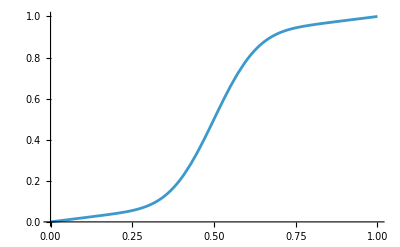
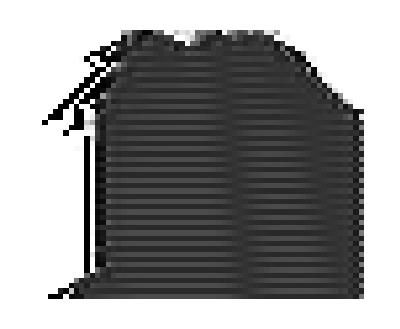
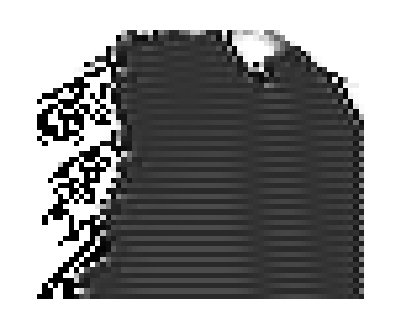

```mathematica
NAND[a_, b_]:=1-a b
NOT[a_]:=NAND[a, a]
AND[a_, b_]:=NOT[NAND[a, b]]
OR[a_, b_]:=NAND[NOT[a], NOT[b]]
XOR[a_, b_]:=AND[OR[a, b], NAND[a, b]]
Code20SingleUnactivated[a_, b_, c_, d_, e_]:=XOR[XOR[a, XOR[b, XOR[c, XOR[d, e]]]], OR[a, OR[b, OR[c, OR[d, e]]]]]

Clear[ActivationFunction]
t[x_]:=(1-Cos[x N[Pi/2]]^2)
ActivationFunction[x_]:=0.8 t[t[t[x]]]+0.2 x

Code20SingleUncompiled[list__]:=ActivationFunction[Code20SingleUnactivated[list]]
Code20RowUncompiled[list_]:=Code20SingleUncompiled@@@Partition[ArrayPad[list,2],5,1]

{
Plot[ActivationFunction[x], {x,0, 1}],ArrayPlot[NestList[Code20RowUncompiled, ArrayPad[RandomReal[{0, 1}, 30], 16], 50]],
ArrayPlot[NestList[Code20RowUncompiled, ArrayPad[RandomReal[{0, 1}, 30], 16], 50]]
}
```

```mathematica
(* Code20Single=
ToExpression["FunctionCompile[Function[{Typed[a, \"Real64\"],Typed[b, \"Real64\"],Typed[c, \"Real64\"],Typed[d, \"Real64\"],Typed[e, \"Real64\"]}, "<>ToString[ActivationFunction[Code20SingleUnactivated[a, b, c, d, e]], InputForm]<>"], CompilerOptions->{\"LLVMOptimization\"->\"ClangOptimization\"[3], \"AbortHandling\"->False, \"OptimizationLevel\"->3,\"InvocationMode\"->\"Standalone\"}]"] *)
Code20Single=ActivationFunction@*Interpolation[{#,Code20SingleUncompiled@@#}&/@Tuples[{0, 1}, 5]]
With[{r=RandomReal[{0, 1}, 5]},First@RepeatedTiming[Code20Single@@r]]
```

Interpolation::inhr: Requested order is too high; order has been reduced to {1,1,1,1,1}.

ActivationFunction@*InterpolatingFunction[…]

6.19097×10^-6

```mathematica
StripZeros[list_]:=list//.{{0, x___}->List@x, {x___, 0}->List@x}
ExpandZeros[list_]:=list//.{{a_?Positive, b_?Positive, x___}->{0, a, b, x}, {x___, a_?Positive, b_?Positive}->{x, a, b, 0}}
```

0.017688

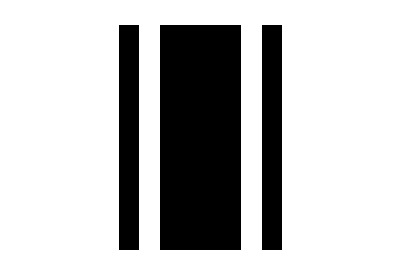
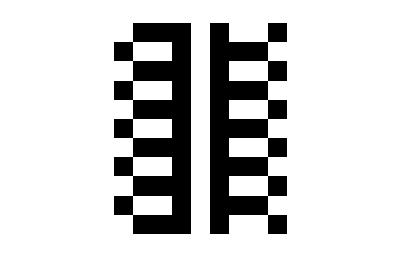
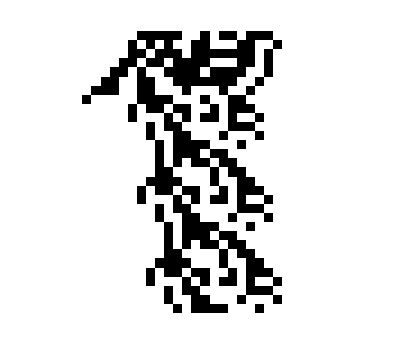
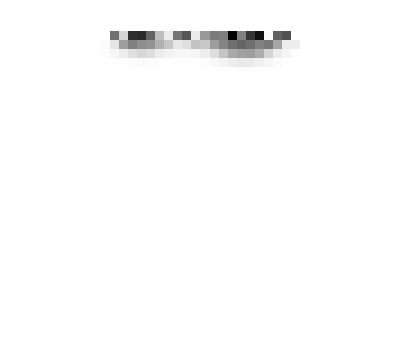

True

12

```mathematica
Code20Row[list_]:=Code20Single@@@Partition[ArrayPad[list,2],5,1]
Code20RowExpanding[list_]:=Code20Row@ExpandZeros[list]

With[{r=RandomInteger[1, 1000]},First[RepeatedTiming[Code20Row[r]]]]
{ArrayPlot[NestList[Code20Row, ArrayPad[{1, 0, 1, 1, 1, 1, 0, 1}, 4], 10]],ArrayPlot[NestList[Code20Row, ArrayPad[{0, 1, 1, 1, 0, 1, 0, 0,1}, 4], 10]],ArrayPlot[NestList[Code20Row, ArrayPad[RandomInteger[{0, 1}, 20], 8], 30]],
ArrayPlot[NestList[Code20Row, ArrayPad[RandomReal[{0, 1}, 20], 8], 30]]
}

With[{r=RandomInteger[1, 1000]},StripZeros@Rationalize@Code20RowExpanding[r]==StripZeros@Last@CellularAutomaton[{20, {2, 1}, 2}, {r, 0}, 1]]

Code20RowExpanding[RandomReal[{0, 1}, 10]]//Length
```

```mathematica
LossPeriodic[p_][list_]:=If[Min[list]<0||Max[list]>1, 100000, With[{periodicitydiff=ArrayPad[list, 2p]-Nest[Code20Row, ArrayPad[list, 2p], p]},(periodicitydiff.periodicitydiff)-Max[list]]]
LossPeriodicBinary[p_][list_]:=If[Min[list]<0||Max[list]>1, 100000, With[{periodicitydiff=ArrayPad[list, 2p]-Nest[Code20Row, ArrayPad[list, 2p], p], closenesstobinary=list * (1-list)},(periodicitydiff.periodicitydiff)+10(closenesstobinary.closenesstobinary)-Max[list]]]

LossPeriodic[1][{1, 0, 1, 1, 1, 1, 0, 1}]
```

-1.

## Testing

{0.,0.,0.157996,0.239446,0.648205,1.,0.248869,0.160664,0.,0.0000674281}

-0.636765

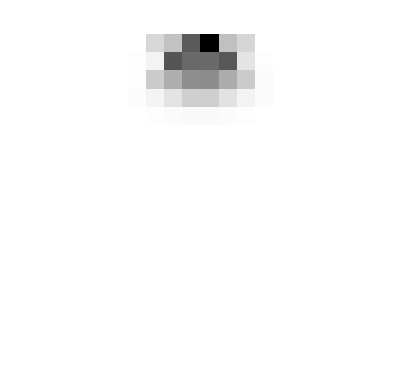

{0.,0.,0.00889018,0.0252824,0.529554,0.988998,0.0258991,0.00941617,0.,0.}

0.148399

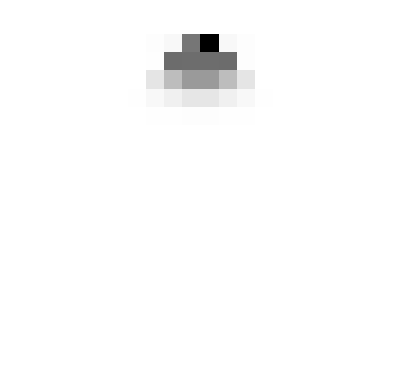

{0,0,0,0,1,1,0,0,0,0}

1.

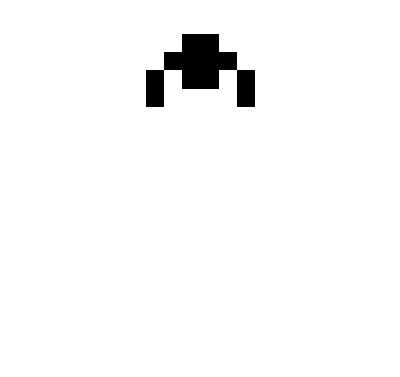

```mathematica
p=2;
n=10;

res2=GradientDescent[LossPeriodic[p],n, "History"->False,"MaxIterations"->1000,"Restarts"->50, "Tolerance"->10^-10];
point2 = res2["Point"]
res2["Loss"]

Labeled[ArrayPlot[NestList[Code20Row, ArrayPad[point2, 2p], 3 p + 10]], "Best Periodicity"]

res3=GradientDescent[LossPeriodicBinary[p],n, "History"->False,"MaxIterations"->10000,"Restarts"->50, "Tolerance"->10^-10, "InitialPoints"->point2];
point3 = res3["Point"]
res3["Loss"]

Labeled[ArrayPlot[NestList[Code20Row, ArrayPad[point3, 2p], 3 p + 10]], "Best Periodicity and Binary"]

point4 = Round[point3]
LossPeriodicBinary[p][point4]

Labeled[ArrayPlot[NestList[Code20Row, ArrayPad[point4, 2p], 3 p + 10]], "Rounded"]
```

```mathematica
LossPeriodic[p][{1, 0, 1, 1, 1, 1, 0, 1}]
```

-1.